```mathematica
4*0.067
```

0.268

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ =- 0.25;  θ=(10Pi/180);
Vddπ2 =1.0; Vddσ2 = -1.5; Vddδ2 = -0.25;    
Vddπn = 1.0*0.07; Vddσn = -1.5*0.07; Vddδn = -0.25*0.07; 
4/3(Vddπ2+Vddδ2)+(4Vddπ2+ (Vddδ2-4 Vddπ2+3 Vddσ2) Cos[2 θ]^2)/3

2/3(Vddδn+Vddπn)+(Vddδn+4 Vddπn+3 Vddσn-(Vddδn-4 Vddπn+3 Vddσn) Cos[4 θ])(1/12)

2/3 (Vddδ+Vddπ) Cos[2 θ]+(1/12)(-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])

2/3 (Vddπ+Vddδ) Sin[2θ]

2/3(Vddπ+Vddδ+Vddπ Sin[2 θ]^2+Vddσ Cos[2θ]^2)
2/3(Vddπn+Vddδn+Vddπn Cos[2 θ]^2+Vddσn Sin[2θ]^2)
2/3((Vddπ+Vddδ) Cos[2θ]+Vddπ Cos[2θ]^2-Vddσ Sin[2θ]^2)
2/3 (Vddπ+Vddδ) Sin[2θ]
```

-0.242148

0.0697252

1.30711

0.17101

-0.305037

0.0680193

1.17551

0.17101

```mathematica
4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)
```

1.33333

-1.

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ = -0.25;  θ=(11Pi/180)+-π/4;  
4/3((Vddπ+Vddδ) Cos[2θ]+Vddσ Cos[2θ]^2-Vddπ Sin[2θ]^2)
```

-1.05228

```mathematica
Vddπ =1.0; Vddσ = -1.5; Vddδ =-0.25;  θ=(11Pi/180);  
2/3(Vddπ+Vddδ+Vddπ Sin[2 θ]^2+Vddσ Cos[2θ]^2)
2/3((Vddπ+Vddδ) Cos[2θ]-Vddσ Sin[2θ]^2+Vddπ Cos[2θ]^2)
Vddπn = 0.07; Vddσn = -1.5*0.07; Vddδn = -0.25*0.07;  θ=(11Pi/180);  
2/3(Vddπn+Vddδn+Vddπn Cos[2 θ]^2+Vddσn Sin[2θ]^2)
```

-0.266117

1.17704

0.0652948

```mathematica
Clear[Vddπ,Vddδ,θ];
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify
Vddπ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddδ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

-Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

-Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
(**)
```

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify
Vddδ Cos[-θ+ϕ]Cos[θ+ϕ]-Vddπ Sin[-θ+ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

-Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

-Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

```mathematica
Clear[Vddπ,Vddδ,θ,Vddσ];
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->0}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π/2}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π}//FullSimplify
Vddπ Cos[2(-θ+ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(-θ+ϕ)]Sin[2(θ+ϕ)]/.{ϕ->3π/2}//FullSimplify
```

Vddπ Cos[2 θ]^2+Vddσ Sin[2 θ]^2

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

```mathematica
(**)
```

Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

```mathematica
Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2-(1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ]))//Simplify
```

0

```mathematica
Cos[2(-π/4+a)]//FullSimplify
```

Sin[2 a]

```mathematica
Solve[2/3(x+Vddδ*x+Vddπ*x Cos[2 θ]^2+Vddσ*x Sin[2θ]^2)==0.066,x]
```

{{x→0.070756}}

```mathematica
Integrate[(Exp[-x/(2*4)] x/4)(Exp[(-(x-2))/(2*4)](x-2)/4),{x,0, Infinity}]//N
Integrate[(Exp[-x/(2*4)] x/4)(Exp[(-(x-4))/(2*4)](x-4)/4),{x,0, Infinity}]//N
```

7.70415

6.59489

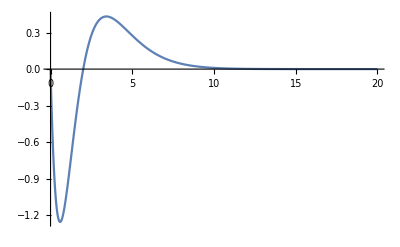

```mathematica
Plot[(Exp[-x/2]x)(Exp[(-(x-2))/2](x-2)),{x,0,20},PlotRange->All]
```

```mathematica
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π}//FullSimplify

Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2}//FullSimplify
```

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

```mathematica
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π}//FullSimplify

Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2}//FullSimplify
```

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

```mathematica
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π}//FullSimplify

Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π/2}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+(3π)/2}//FullSimplify
```

1/2 (Vddπ+Vddσ+(-Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(-Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(-Vddπ+Vddσ) Cos[4 θ])

«1 more identical outputs»

```mathematica
(1-Cos[4θ])/2 //FullSimplify
(1+Cos[4θ])/2 //FullSimplify
```

Sin[2 θ]^2

Cos[2 θ]^2

```mathematica
Exp[-I(kx+ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[I(kx+ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[I(kx-ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[-I(kx-ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[-I(kx+ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[I(kx+ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[I(kx-ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[-I(kx-ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))//FullSimplify
```

4 (Vddδ+Vddπ) Cos[kx] Cos[ky]

```mathematica
Exp[-I(kx+ky)]a+Exp[I(kx+ky)]a+Exp[I(kx-ky)]a+Exp[-I(kx-ky)]a//FullSimplify
```

4 a Cos[kx] Cos[ky]

```mathematica
Clear[Vddπ,Vddδ,θ];
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4,θ->π/4+θ}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π,θ->π/4+θ}//FullSimplify

Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2,θ->π/4+θ}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2,θ->π/4+θ}//FullSimplify
```

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

```mathematica
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4,θ->π/4+θ}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π,θ->π/4+θ}//FullSimplify

Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2,θ->π/4+θ}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2,θ->π/4+θ}//FullSimplify
```

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

```mathematica
Clear[Vddπ,Vddδ,Vddσ,θ];
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4,θ->π/4+θ}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π,θ->π/4+θ}//FullSimplify

Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π/2,θ->π/4+θ}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+(3π)/2,θ->π/4+θ}//FullSimplify
```

Vddπ Cos[2 θ]^2+Vddσ Sin[2 θ]^2

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

```mathematica
Exp[-I(kx+ky)](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[I(kx+ky)](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[I(kx-ky)](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[-I(kx-ky)](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[-I(kx+ky)](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[I(kx+ky)](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[I(kx-ky)](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[-I(kx-ky)](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)//FullSimplify
```

4 (Vddδ+Vddπ) Cos[kx] Cos[ky]

```mathematica
Clear[Vddπ,Vddδ,θ];
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4,θ->(3π)/4+θ}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π,θ->(3π)/4+θ}//FullSimplify

Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2,θ->(3π)/4+θ}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2,θ->(3π)/4+θ}//FullSimplify
```

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

```mathematica
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4,θ->(3π)/4+θ}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π,θ->(3π)/4+θ}//FullSimplify

Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2,θ->(3π)/4+θ}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2,θ->(3π)/4+θ}//FullSimplify
```

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

```mathematica
Clear[Vddπ,Vddδ,Vddσ,θ];
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4,θ->(3π)/4+θ}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π,θ->(3π)/4+θ}//FullSimplify

Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+π/2,θ->(3π)/4+θ}//FullSimplify
Vddπ Cos[2(θ-ϕ)]^2+Vddσ Sin[2(θ-ϕ)]^2/.{ϕ->π/4+(3π)/2,θ->(3π)/4+θ}//FullSimplify
```

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

Vddπ Cos[2 θ]^2+Vddσ Sin[2 θ]^2

1/2 (Vddπ+Vddσ+(Vddπ-Vddσ) Cos[4 θ])

```mathematica
Clear[Vddπ,Vddδ,θ];
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->0}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π}//FullSimplify

Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/2}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->3 π/2}//FullSimplify
```

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

```mathematica
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify

Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify

Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

```mathematica
Clear[Vddσ];
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->0}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π/2}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->3π/2}//Simplify
```

Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ+(Vddπ+Vddσ) Cos[4 θ])

```mathematica
Exp[-I kx](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[I kx](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[-I ky](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[I ky](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[-I kx](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[I kx](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[-I ky](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[I ky](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[-I kx](Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2)+Exp[I kx](Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2)+Exp[-I ky](Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2)+Exp[I ky](Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2)//FullSimplify
```

(Cos[kx]+Cos[ky]) (Vddπ-Vddσ+2 (Vddδ+Vddπ) Cos[2 θ]+(Vddπ+Vddσ) Cos[4 θ])

```mathematica
(Vddπ-Vddσ+2 (Vddδ+Vddπ) Cos[2 θ]+(Vddπ+Vddσ) Cos[4 θ])/2-(Vddπ Cos[2 θ]^2-Vddσ Sin[2 θ]^2+(Vddδ+Vddπ)Cos[2θ])//Simplify
```

0

```mathematica
Cos[4 θ]//TrigFactor
```

2 Sin[π/4-2 θ] Sin[π/4+2 θ]

```mathematica
Clear[θ,Vddπ,Vddδ];

Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0,θ->θ+π/4}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π,θ->θ+π/4}//Simplify

Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2,θ->θ+π/4}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2,θ->θ+π/4}//Simplify
```

1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ])

```mathematica
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0,θ->θ+π/4}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π,θ->θ+π/4}//Simplify

Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2,θ->θ+π/4}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2,θ->θ+π/4}//Simplify
```

1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ])

1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ])

```mathematica
Clear[Vddσ];
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->0,θ->θ+π/4}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π,θ->θ+π/4}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->π/2,θ->θ+π/4}//Simplify
Vddπ Cos[2(θ-ϕ)]Cos[2(θ+ϕ)]-Vddσ Sin[2(θ-ϕ)]Sin[2(θ+ϕ)]/.{ϕ->3π/2,θ->θ+π/4}//Simplify
```

1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ])

1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ])

«1 more identical outputs»

```mathematica
Exp[-I kx](1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[I kx](1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[-I ky](1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[I ky](1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[-I kx](1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[I kx](1/2 (Vddδ-Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[-I ky](1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[I ky](1/2 (-Vddδ+Vddπ-(Vddδ+Vddπ) Sin[2 θ]))+Exp[-I kx](1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ]))+Exp[I kx](1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ]))+Exp[-I ky](1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ]))+Exp[I ky](1/2 (Vddπ-Vddσ-(Vddπ+Vddσ) Cos[4 θ]))//FullSimplify
```

-(Cos[kx]+Cos[ky]) (-Vddπ+Vddσ+(Vddπ+Vddσ) Cos[4 θ]+2 (Vddδ+Vddπ) Sin[2 θ])

```mathematica
-(-Vddπ+Vddσ+(Vddπ+Vddσ) Cos[4 θ]+2 (Vddδ+Vddπ) Sin[2 θ])/3//FullSimplify
```

0.76592

```mathematica
Clear[Vddπ,θ,Vddδ];
-Vddπ Cos[θ-ϕ]Sin[θ+ϕ]-Vddδ Cos[θ+ϕ]Sin[θ-ϕ]/.{ϕ->0}
-Vddπ Cos[θ-ϕ]Sin[θ+ϕ]-Vddδ Cos[θ+ϕ]Sin[θ-ϕ]/.{ϕ->π}

-Vddπ Cos[θ-ϕ]Sin[θ+ϕ]-Vddδ Cos[θ+ϕ]Sin[θ-ϕ]/.{ϕ->π/2}
-Vddπ Cos[θ-ϕ]Sin[θ+ϕ]-Vddδ Cos[θ+ϕ]Sin[θ-ϕ]/.{ϕ->3π/2}
```

-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ]

-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ]

-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ]

«1 more identical outputs»

```mathematica
Vddπ Sin[θ-ϕ]Cos[θ+ϕ]+Vddδ Cos[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0}
Vddπ Sin[θ-ϕ]Cos[θ+ϕ]+Vddδ Cos[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π}

Vddπ Sin[θ-ϕ]Cos[θ+ϕ]+Vddδ Cos[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2}
Vddπ Sin[θ-ϕ]Cos[θ+ϕ]+Vddδ Cos[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}
```

Vddδ Cos[θ] Sin[θ]+Vddπ Cos[θ] Sin[θ]

Vddδ Cos[θ] Sin[θ]+Vddπ Cos[θ] Sin[θ]

Vddδ Cos[θ] Sin[θ]+Vddπ Cos[θ] Sin[θ]

«1 more identical outputs»

```mathematica
Exp[-I kx](-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ])+Exp[I kx](-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ])+Exp[-I ky](-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ])+Exp[I ky](-Vddδ Cos[θ] Sin[θ]-Vddπ Cos[θ] Sin[θ])//FullSimplify
```

-(Vddδ+Vddπ) (Cos[kx]+Cos[ky]) Sin[2 θ]

```mathematica
3 l^2 m^2 Vddσ+(l^2+m^2-4 l^2 m^2)Vddπ+(n^2+l^2 m^2)Vddδ/.{l->Cos[ϕ]Sin[θ],m->Sin[ϕ]Sin[θ],n->Cos[θ]}//FullSimplify
```

```mathematica
Vddδ Cos[θ]^2+Vddπ Sin[θ]^2+(Vddδ-4 Vddπ+3 Vddσ) Cos[ϕ]^2 Sin[θ]^4 Sin[ϕ]^2/.{θ->π/2}
```

Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[ϕ]^2 Sin[ϕ]^2

```mathematica
3 l^2 m^2 Vddσ+(l^2+m^2-4 l^2 m^2)Vddπ+(n^2+l^2 m^2)Vddδ/.{l->Sin[ϕ]Sin[θ],m->Cos[θ],n->Cos[ϕ]Sin[θ]}//FullSimplify
```

```mathematica
Vddπ Cos[θ]^2+Vddδ Cos[ϕ]^2 Sin[θ]^2+((Vddδ+3 Vddσ) Cos[θ]^2-Vddπ (1+2 Cos[2 θ])) Sin[θ]^2 Sin[ϕ]^2/.{θ->π/2}//FullSimplify
```

Vddδ Cos[ϕ]^2+Vddπ Sin[ϕ]^2

```mathematica
3 l^2 m^2 Vddσ+(l^2+m^2-4 l^2 m^2)Vddπ+(n^2+l^2 m^2)Vddδ/.{l->Cos[θ],m->Cos[ϕ]Sin[θ],n->Sin[ϕ]Sin[θ]}//FullSimplify
```

```mathematica
Cos[θ]^2 (Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[ϕ]^2 Sin[θ]^2)+Sin[θ]^2 (Vddπ Cos[ϕ]^2+Vddδ Sin[ϕ]^2)/.{θ->π/2}//FullSimplify
```

Vddπ Cos[ϕ]^2+Vddδ Sin[ϕ]^2

```mathematica
Cos[θ]^2 Sin[θ]^2-(Sin[2θ]^2)/4//FullSimplify
```

0

```mathematica
(2/√3)^5//N
```

2.0528

```mathematica
-0.93/(2/√3)^5//N
```

-0.45304

```mathematica
2/√3//N
```

1.1547

```mathematica
1/(√2)^5//N
```

0.176777

```mathematica
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/4}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/4+π}//Simplify

Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/4+π/2}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/4+3π/2}//Simplify
```

Vddπ+1/4 (Vddδ-4 Vddπ+3 Vddσ) Cos[2 θ]^2

Vddπ+1/4 (Vddδ-4 Vddπ+3 Vddσ) Cos[2 θ]^2

Vddπ+1/4 (Vddδ-4 Vddπ+3 Vddσ) Cos[2 θ]^2

«1 more identical outputs»

```mathematica
Exp[-I(kx+ky)]a+Exp[I(kx+ky)]a+Exp[I(kx-ky)]a+Exp[-I(kx-ky)]a//FullSimplify
```

4 a Cos[kx] Cos[ky]

```mathematica
4Vddπ+ (Vddδ-4 Vddπ+3 Vddσ) Cos[2 θ]^2
```

```mathematica
1/2^5//N
1/(√2)^5//N
```

0.03125

0.176777

```mathematica
Print["yz-orbital σ0τ0 components"]
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2}//FullSimplify
```

yz-orbital σ0τ0 components

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

```mathematica
Print["zx-orbital σ0τ0 components"]
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+π/2}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/4+3 π/2}//FullSimplify
```

zx-orbital σ0τ0 components

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ])

```mathematica
Exp[-I(kx+ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[I(kx+ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[I(kx-ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[-I(kx-ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[-I(kx+ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[I(kx+ky)](1/2 (Vddδ+Vddπ+(Vddδ-Vddπ) Sin[2 θ]))+Exp[I(kx-ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))+Exp[-I(kx-ky)](1/2 (Vddδ+Vddπ+(-Vddδ+Vddπ) Sin[2 θ]))//FullSimplify
```

4 (Vddδ+Vddπ) Cos[kx] Cos[ky]

```mathematica
Exp[-I(kx+ky)]a+Exp[I(kx+ky)]a+Exp[I(kx-ky)]a+Exp[-I(kx-ky)]a//FullSimplify
```

4 a Cos[kx] Cos[ky]

```mathematica
Clear[Vddπ,Vddδ,θ];
Print["yz-orbital σ0τ0 components 2nd nearest"]
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->0}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->π/2}//FullSimplify
Vddπ Cos[θ-ϕ]^2+Vddδ Sin[θ-ϕ]^2/.{ϕ->3 π/2}//FullSimplify
```

yz-orbital σ0τ0 components 2nd nearest

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

```mathematica
Print["zx-orbital σ0τ0 components 2nd nearest"]

Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->0}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->π/2}//FullSimplify
Vddδ Cos[θ-ϕ]^2+Vddπ Sin[θ-ϕ]^2/.{ϕ->3 π/2}//FullSimplify
```

zx-orbital σ0τ0 components 2nd nearest

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddδ Cos[θ]^2+Vddπ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

Vddπ Cos[θ]^2+Vddδ Sin[θ]^2

```mathematica
Exp[-I kx](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[I kx](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[-I ky](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[I ky](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[-I kx](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[I kx](Vddδ Cos[θ]^2+Vddπ Sin[θ]^2)+Exp[-I ky](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)+Exp[I ky](Vddπ Cos[θ]^2+Vddδ Sin[θ]^2)//FullSimplify
```

2 (Vddδ+Vddπ) (Cos[kx]+Cos[ky])

```mathematica
Print["xy-orbital σ0τ0 components 2nd nearest"]
```

```mathematica
Clear[Vddσ];
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->0}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π}//Simplify

Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/2}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ-θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->3π/2}//Simplify
```

Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2

Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2

Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2

«1 more identical outputs»

```mathematica
Exp[-I kx](Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2)+Exp[I kx](Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2)+Exp[-I ky](Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2)+Exp[I ky](Vddπ+(Vddδ-4 Vddπ+3 Vddσ) Cos[θ]^2 Sin[θ]^2)//FullSimplify
```

1/4 (Cos[kx]+Cos[ky]) (Vddδ+4 Vddπ+3 Vddσ-(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])

```mathematica
2/3(Vddδ+Vddπ)+(Vddδ+4 Vddπ+3 Vddσ-(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])(1/12)
```

```mathematica
Print["yz orbital τx components"]
```

```mathematica
Clear[Vddπ, Vddδ,θ];
Print["yz orbital τx components"]
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify

Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddπ Cos[θ-ϕ]Cos[θ+ϕ]-Vddδ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

yz orbital τx components

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

```mathematica
Print["zx orbital τx components"]
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->0}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π}//Simplify

Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->π/2}//Simplify
Vddδ Cos[θ-ϕ]Cos[θ+ϕ]-Vddπ Sin[θ-ϕ]Sin[θ+ϕ]/.{ϕ->3π/2}//Simplify
```

zx orbital τx components

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddδ Cos[θ]^2-Vddπ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

Vddπ Cos[θ]^2-Vddδ Sin[θ]^2

```mathematica
Exp[-I kx](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[I kx](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[-I ky](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[I ky](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[-I kx](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[I kx](Vddδ Cos[θ]^2-Vddπ Sin[θ]^2)+Exp[-I ky](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)+Exp[I ky](Vddπ Cos[θ]^2-Vddδ Sin[θ]^2)//FullSimplify
```

2 (Vddδ+Vddπ) (Cos[kx]+Cos[ky]) Cos[2 θ]

```mathematica
Clear[Vddσ];
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ+θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->0}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ+θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π}//Simplify

Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ+θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->π/2}//Simplify
Vddπ+1/4 Sin[2(ϕ-θ)]Sin[2(ϕ+θ)](3Vddσ+Vddδ-4Vddπ)/.{ϕ->3π/2}//Simplify
```

Vddπ-1/4 (Vddδ-4 Vddπ+3 Vddσ) Sin[2 θ]^2

Vddπ-1/4 (Vddδ-4 Vddπ+3 Vddσ) Sin[2 θ]^2

1/8 (-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])

1/8 (-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])

```mathematica
Exp[-I kx](Vddπ-1/4 (Vddδ-4 Vddπ+3 Vddσ) Sin[2 θ]^2)+Exp[I kx](Vddπ-1/4 (Vddδ-4 Vddπ+3 Vddσ) Sin[2 θ]^2)+Exp[-I ky](1/8 (-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ]))+Exp[I ky](1/8 (-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ]))//FullSimplify
```

1/4 (Cos[kx]+Cos[ky]) (-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])

```mathematica
2/3 (Vddδ+Vddπ) Cos[2 θ]+(1/12)(-Vddδ+12 Vddπ-3 Vddσ+(Vddδ-4 Vddπ+3 Vddσ) Cos[4 θ])
```